# Advance Math Modeling Project Technical Report

## Harmonization Project

## Selim Karaoglu

## Introduction

This project is about music, more specifically, harmonization; we present our method to provide musical harmony between a user selected chord progression and randomly created melody. First  part of this project focuses on chord progression. This module requires 3 inputs from user to create the user selected chord progression: root note, scale and chord arrangement. Furthermore, a random melody is created within 2 octave range from the given root note. Finally, this random created melody is evolved with our harmonization function to have harmony with the previously designed chord progression.  The function that harmonizes the random melody and user selected chord progression is based on basic music theory and some commonly accepted approaches in modern music.

Statement of the original problem: Music creation process sometimes require inspiration. When a musician creates the chord progression for his work but needs a melody, there are not many different sources that can prove helpful. For such scenario, designing a method that creates random but musically meaningful melodies for a given chord progression might be a solution.

Problem Analysis: This problem requires a method to create random melodies that are in harmony with provided chord progression. Following a piece-to-whole approach; this problem is based on a melody and a chord progression. These two elements share a root note, a scale and tempo of the music. The melody can be explained deeper with individual notes. The chord progressions are based on the root note, scale and the chord arrangement. These three pieces of the chord progression information should be obtained from the users. With this information in hand, it is possible to create random melodies that are harmonized with the given chord progression.

Assumptions and Simplifications: Musical preferences are unique for each people, therefore there is no single formula that would work for every musical piece. There are some guidelines and commonly accepted methods that can provide harmonization. We assume that users of this project are making music based on classical Western music theory. There are different musical scales adopted in classical Western music, although the modern Western music mostly employ the minor and major scales, consequently we developed our methods based on these two scales. Another important part of this process is chord arrangement. There are infinite possible chord arrangements, but based on their appearances, some chord arrangements are very popular in modern music. Since these chord arrangements are dependant on the root note and the scale, there are two groups of chord arrangement defined for each scale. Selected minor chord arrangements are named pop progression (due to it’s popularity in modern pop music), 50’s progression (due to it’s popularity in 50’s) and Andalusian cadence (widely accepted throughout time by many different cultures) and major chord arrangements are pop progression and Andalusian cadence. Many different chord progressions can be included in this list, however due to our time duration design we limit our selection with chord arrangements that contain 4 chords. Finally, the harmonization of the random created melody and given chord progression is provided with the classical Western music theory, therefore the assumption that makes harmonized melody “better” or “fitter” comes from the classical Western music theory.

## Background

To develop the harmonization model, we employed built-in Mathematica functions. The Sound function provides playable outputs with given parameters. The SoundNote function creates musical instrument sounds with given note names and time durations. To explain the project in detail, here we provide some background information on basic music theory and technical details adopted in the development process.

### Note

In music theory, note represents the musical sound based on a pitch and a time duration. A single note is the most basic element of this project. Both chord progression and melody are both based on creation of notes in a certain way. The notation of the musical notes in modern music is provided with Latin letters from A to G and there are 12 notes in classical Western music. The notes are  named as “C, C#, D, D#, E, F, F#, G, G#, A, A#, B” (given in C major scale order). In Mathematica, to play a musical note, SoundNote function can be utilized with pitch and time duration parameters. The middle C note (on a 88 key piano ) is represented with string value “C4” or with integer 0. Here we create two SoundNotes in a Sound function; the first note is created with only 0 as a parameter and the second note is created with only “C4”, no time duration specified (default  is 1 second). Below figure shows middle C note. To hear the sound produced by Mathematica’s Sound function, users required to press the blue play button. The total time of the sound is shown on the right bottom corner of the output.

-Graphics-

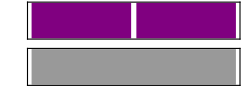

```mathematica
Sound[{SoundNote[0], SoundNote["C4"]}]
```

The note names presented above shows that the note A is 9 notes further from the note C, consequently creating a sound note with pitch parameter set to 9 will yield middle A note. Below example shows, these three different parameters yield the same result. This provides the option of treating notes with numerical values, making it easier to understand.

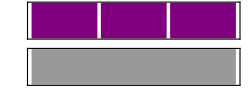

```mathematica
Sound[{SoundNote[9], SoundNote["A"], SoundNote["A4"]}]
```

### Scale

Scale is a musical concept that a group of notes are ordered according to their pitch in a specific way. The musical scale is a key element to design musical harmony between different instruments playing simultaneously owing to the fact that it provides a guideline for what notes are meant to be played. A musical scale is defined by a sequence and a root note, also known as signature key. The scale is defined by starting from the root note and following the note sequence until reaching the same note’s lower pitch; an octave. In modern Western music, there are 12 notes within an octave. Below figure shows every note between middle C to the higher octave of middle C (represented with “C5” or integer 12) in musical notation form. This result can be referred as C chromatic scale.

```mathematica
-Graphics-
-Graphics-
```

Here we create these outputs that allow us to hear musical notes in C chromatic scale with functions provided by Mathematica.

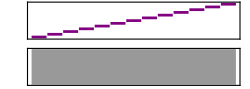

```mathematica
Sound[Table[SoundNote[i],{i,0,12}]]
```

In different styles of music, there are many different scales adopted by different civilizations, societies and cultures. Contemporary mainstream music products employ many different musical scales, although they are mainly focused on two scales (and their variations); minor and major scales. Minor scale contains 7 different notes in an octave. These notes are; the root note and the notes that are 2, 3,5,7,8 and 10 steps away from this note. Similarly, major scale also have 7 notes in an octave consisting of the root note and the notes that are 2,4,5,7,9 and 10 steps away from the root note. In a scenario where the middle C is the root note; following the scale designs, the C minor scale contains notes C, D, D#, F, G, G#, A# and the C major scale contain notes C, D, E, F, G, A, B.  Comparing these two scales, we can see that the difference between these two scales are the (starting from root note) third,  sixth and seventh elements. Figures presented below shows the musical notation of the C minor and C major scales (the last note is the octave, higher C note).

Here we provide the sequences needed to define 4 different scales; minor scale, major scale, minor blues scale and minor pentatonic scale. Following code provides the given scale for middle C.

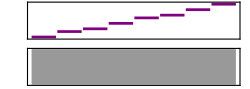

```mathematica
minorscale={0,2,3,5,7,8,10,12};
majorscale = {0,2,4,5,7,9,11,12};
minorbluesscale = {0,3,5,6,7,10,12};
minorpentatonicscale = {0,3,5,7,10,12};
Sound[Table[SoundNote[i],{i,minorscale}]]
```

### Chord

Chord in music refers to a set of at least three different notes (triads that consist of root note, third and fifth intervals higher than the root note) played simultaneously, broken apart or in an arpeggio. The notes in a chord are selected from a scale, this scale name is used to identify the chord name. For example, A minor chord is built with notes A, C and E. Modern musical notation presents chords in a simple way, the major chords are named with capital letters only and the minor chords are added (lowercase) “min” suffix to the chord’s key note. Below output is the Amin chord.

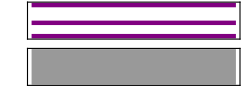

```mathematica
Sound[SoundNote[{"A", "C5","E5"}]]
```

Same Amin chord can be created by assigning root note to 9, adding the note C which is 3 steps away and the note E which is 7 steps away from the root note A.

```mathematica
rootnote = 9;
Sound[SoundNote[Table[i +rootnote,{i,{0,3,7}}]]]
```

-Graphics-

Here we define three functions that will produce the chords needed to create the chord arrangement. These functions can create minor, major and dominant 7th chords.

```mathematica
rootnote = 9;
createminorchord[root_] := {root, root+minorscale[[3]],root+minorscale[[5]]};
minorchord = createminorchord[rootnote];
Sound[SoundNote[Table[i ,{i,minorchord}]]]
```

-Graphics-

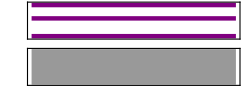

```mathematica
createmajorchord[root_] := {root,root+majorscale[[3]],root+majorscale[[5]]};
majorchord = createmajorchord[rootnote];
Sound[SoundNote[Table[i ,{i,majorchord}]]]
```

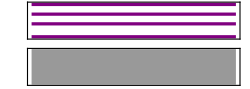

```mathematica
(*Dominant 7th chord is addition of minor 7th to the major chord*)
createdominant7thchord[root_] := {root,root+majorscale[[3]],root+majorscale[[5]],root+minorscale[[7]]};
dominant7thchord=createdominant7thchord[rootnote];
Sound[SoundNote[Table[i ,{i,dominant7thchord}]]]
```

```mathematica
Sound[SoundNote[{10,13,17}]]
```

-Graphics-

### Time Durations

Classical Western music notation shows two specific information for a note; pitch and time duration. The time duration is determined by the tempo of the musical piece, in classical Western music notation, this information is provided on the top of the music sheet. Tempo refers to the beats played in a minute, with this information, notes are even further divided from a single beat that occupies the entire  4/4 measure of time.  This single beat is referred as a whole note. If this note is divided into two notes in the same time interval, we would have half notes. Quarter notes are quarter of the whole notes and sixteenth notes are 1/16 of the whole note. In addition to these, there are also dotted notes;  the notes that are extended another half of the given time duration. We only included a dotted quarter note for this project. Given the note’s time duration and tempo; a whole note yields to (60/tempo)*4. The other notes can be calculated by dividing this duration in halves further.

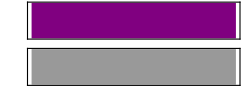

```mathematica
bpm = 120;
quarternote := 60/bpm;
halfnote :=60*2/bpm;
wholenote := 60*4/bpm;
sixteenthnote := 60/(bpm*2);
quarternotedot := 60*3/(2*bpm);
Sound[SoundNote[0,quarternote]]
```

### Chord Arrangement

The chord arrangement is the last information we asked from the users. For minor and major scales, we defined some widely known chord progressions that are utilized in different musical genres. For the major scale, 3 chord progressions implemented are:
	- the Pop progression (I-V-vi-IV)
	- the 50s progression (I-vi-IV-V)
	- the Andalusian Cadence (vi-V-IV-III7).
For the minor scale, the chord arrangements selected are:
	- the Pop progression (i-VI-III-VII)
	- the Andalusian Cadence (i-VII-VI-V7).
Here an important note is, Capital Roman numbers correspond to major while lowercase Roman numbers stand for minor chords (this notation is used when the root note is not known).

#### Major chord progressions

```mathematica
(*Pop progression: I-V-vi-IV*)
(*50s progression: I-vi-IV-V*)
(*Andalusian Cadence: vi-V-IV-III7*)
majorpop[root_] := {
SoundNote[Table[i+root, {i,majorchord}],{0,wholenote}],
SoundNote[Table[i+root-5, {i,majorchord}],{wholenote,2*wholenote}],
SoundNote[Table[i+root-3, {i,minorchord}],{2*wholenote,3*wholenote}],
SoundNote[Table[i+root-7, {i,majorchord}],{3*wholenote,4*wholenote}]
};
fifties[root_]:= {
SoundNote[Table[i+root, {i,majorchord}],{0,wholenote}],
SoundNote[Table[i+root-3, {i,minorchord}],{wholenote,2*wholenote}],
SoundNote[Table[i+root-7, {i,majorchord}],{2*wholenote,3*wholenote}],
SoundNote[Table[i+root-5, {i,majorchord}],{3*wholenote,4*wholenote}]
};
majorandalusian[root_]:= {
SoundNote[Table[i+root-3, {i,minorchord}],{0,wholenote}],
SoundNote[Table[i+root-5, {i,majorchord}],{wholenote,2*wholenote}],
SoundNote[Table[i+root-7, {i,majorchord}],{2*wholenote,3*wholenote}],
SoundNote[Table[i+root-8, {i,dominant7thchord}],{3*wholenote,4*wholenote}]
};
```

#### Minor chord progressions

```mathematica
(*Pop progression: i-VI-III-VII*)
(*Andalusian cadence: i-VII-VI-V7*)
minorpop[root_]:= {
SoundNote[Table[i+root, {i,minorchord}],{0,wholenote}],
SoundNote[Table[i+root-4, {i,majorchord}],{wholenote,2*wholenote}],
SoundNote[Table[i+root+3, {i,majorchord}],{2*wholenote,3*wholenote}],
SoundNote[Table[i+root-2, {i,majorchord}],{3*wholenote,4*wholenote}]
};
minorandalusian[root_]:= {
SoundNote[Table[i+root, {i,minorchord}],{0,wholenote}],
SoundNote[Table[i+root-2, {i,majorchord}],{wholenote,2*wholenote}],
SoundNote[Table[i+root-4, {i,majorchord}],{2*wholenote,3*wholenote}],
SoundNote[Table[i+root-5, {i,dominant7thchord}],{3*wholenote,4*wholenote}]
};
```

By using the provided root note, scale and chord arrangement informations, we can create a chord progression that is as long as  4 of 4/4 bars with given tempo, in other words 4 whole notes. The selected chord arrangements are all based on 4 chords, therefore each chord takes the time of a single 4/4 bar or a whole note.  For example, if a user designs a chord progression based on 120 bpm tempo, root note A, minor scale and minor Andalusian Cadence, the complete chord progression would take exactly 8 seconds since(120/60*4) is equal to 8. The time duration for the complete chord progression is shown on the bottom right corner of the Sound function result.

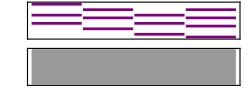

```mathematica
bpm=120;
Sound[minorandalusian[9]]
```

Fur Elise Example:
To show an example to a harmonization of a melody and a chord progression, we demonstrate the beginning of the musical piece “Fur Elise” composed by Ludwig van Beethoven. This song is written on A minor key (root note A and minor scale), therefore we added the dominant 7th of E (the fifth interval) and A minor chords to create the chord arrangement.

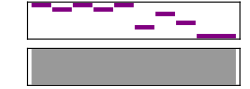

```mathematica
bpm = 120;
Sound[{
SoundNote["E",sixteenthnote],
SoundNote["D#", sixteenthnote],
SoundNote["E",sixteenthnote],
SoundNote["D#", sixteenthnote],
SoundNote["E",sixteenthnote],
SoundNote["B3", sixteenthnote],
SoundNote["D",sixteenthnote],
SoundNote["C", sixteenthnote],
SoundNote["A3",quarternote]
}]
```

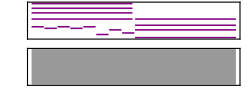

```mathematica
rootnote =4;
bpm=120;
melody = {SoundNote["E",sixteenthnote],SoundNote["D#", sixteenthnote],SoundNote["E",sixteenthnote],SoundNote["D#", sixteenthnote],SoundNote["E",sixteenthnote],SoundNote["B3", sixteenthnote],SoundNote["D",sixteenthnote],SoundNote["C", sixteenthnote],SoundNote["A3",wholenote]};
chords = {SoundNote[Table[i, {i,dominant7thchord}],{0,wholenote}],SoundNote[Table[i-7, {i,minorchord}],{wholenote,2*wholenote}]};
Sound[Flatten[{melody,chords}]]
```

## Methodology

This section provides insight about the random melody creation process and harmonization of this randomly created melody and user defined chord progression. First we introduce the random melody creation with the time duration creation and randomly assigning notes. Further we explain our harmonization method and produce a randomly created melody that is in harmony with users choice.

### Random Melody Creation

To produce a random melody, we create note durations for a 4 bars with 4/4 time signature. This note durations are created with certain weights assigned to each possible time duration for a note. The time durations utilized in the melody creation are;  whole notes, half notes, quarter with dot notes, quarter notes and sixteenth notes. The weights assigned to these notes are 1 ,2 ,0.5, 3 and 3.5 respectively. These weights are designed to represent the modern music style. We create random values with given time duration weights. After the time durations created, we assign pitch values for each time duration to create notes in the melody. The pitches are selected from 2 octave range from root note randomly.

#### Time Durations

Weights for time durations:

```mathematica
(*For 5 different note durations*)
probsixteenth:=0.35;
probquarter :=0.65;
probhalf:=0.85;
probwhole:=0.95;
probquarterdot:=1;
```

makenote function takes the random integer and returns the time duration.

```mathematica
(*Probabilities;
Sixteenth:%35,
Quarter:%30,
Half:%20,
Whole:%10,
Quarter Dot:%5*)
makenote[nb_, bpm_]:=Module[{n=nb, b=bpm},
quarternote := 60/bpm;
halfnote :=60*2/bpm;
wholenote := 60*4/bpm;
sixteenthnote := 60/(bpm*2);
quarternotedot := 60*3/(2*bpm);
r:=
If[n≤probsixteenth,sixteenthnote,
If[n≤probquarter,quarternote,
If[n≤probhalf,halfnote,
If[n≤probwhole,wholenote,
If[n≤probquarterdot,quarternotedot]]]]];
Return[r]
]
```

createnotedurations function produces a list random time durations equal to 4 whole notes:

```mathematica
createnotedurations[bpm_]:=Module[{x=bpm},
notedurations:={};
While[4*4*60/x-Plus@@notedurations>0,
n:=RandomReal[{0.00001,1}];
cur:=makenote[n,x];
AppendTo[notedurations,cur]
];
a=Plus@@notedurations;
If[a>4*4*60/x,
notedurations=Drop[notedurations,-1];
AppendTo[notedurations,4*4*60/x-Plus@@notedurations]
];
Return[notedurations]]
```

```mathematica
notedurations = createnotedurations[120]
```

{1/4,2,1,1,1/4,1/4,1/2,1,1/2,1/4,3/4,1/4}

```mathematica
Plus@@notedurations
```

8

```mathematica
4*wholenote
```

8

#### Create Notes with Random Pitch

By iterating over the previously created time durations, we assign random pitches selected from 2 octave range of the root note and add 2 extra notes for possibility of a silent note (musical rest). For minor and major scales, the probability of a note being silent in this method is equal to 1/13.

```mathematica
createrandompitches[dura_,root_] := Module[{x=dura},
(*Create 2 octaves of random pitches*)
notes:={};
(*Added 2 extra integers to list for silent notes. These will be converted to -1*)
Do[AppendTo[notes,RandomInteger[{root,root+26}]],Length[x]];
(*Convert silent notes to -1*)
i=1;
While[i<Length[notes],
If[notes[[i]]>root+24,
notes[[i]]=-1];
i++
];
Return[notes]
];
notes = createrandompitches[notedurations,rootnote];
notes
```

{10,-1,24,14,-1,10,14,11,27,12,-1,11}

#### Random Melody

Here we create a random melody by utilizing the methods shown above.

```mathematica
bpm=60;
rootnote = 9;
createmelody[notes_,notedurations_]:=Module[{x=notes},
melody :={};
Do[AppendTo[melody,SoundNote[x[[i]],notedurations[[i]]]],{i,1,Length[x]}];
Return[melody]
]
```

{10,-1,24,14,-1,10,14,11,27,12,-1,11}

{1/4,2,1,1,1/4,1/4,1/2,1,1/2,1/4,3/4,1/4}

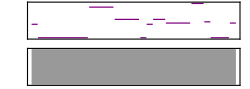

```mathematica
melody = createmelody[notes,notedurations];
Print[notes];
Print[notedurations];
Sound[melody]
```

### Harmonization

The randomly created melody might or might not be in harmony with user selected chord progression. First we need to see if there are any notes in the random melody that is not in harmony. Each note in the random melody is controlled whether they are in the selected scale or not.

#### Find notes out of scale

First we define the notes that are in the given scale for 2 octave range, scalenotes function produces the desired output for given root note and scale:

```mathematica
scalenotes[root_, scale_] :=
If[scale ==minorscale,Flatten[Join[{minorscale,Drop[(minorscale+12),1]}]]+root,
If[scale ==majorscale,Flatten[Join[{majorscale,Drop[(majorscale+12),1]}]]+root,
If[scale ==minorbluesscale,Flatten[Join[{minorbluesscale,Drop[(minorbluesscale+12),1]}]]+root,
If[scale ==minorpentatonicscale, Flatten[Join[{minorpentatonicscale,Drop[(minorpentatonicscale+12),1]}]]+root]]]];
scalenotes[rootnote,minorscale]
```

{9,11,12,14,16,17,19,21,23,24,26,28,29,31,33}

Example of E minor scale notes for 2 octave range:

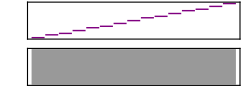

```mathematica
rootnote=4;
Sound[Table[SoundNote[i],{i,scalenotes[rootnote, minorscale]}]]
```

Since we have the scalenotes function, we can employ it to compare random melody with the user defined scale. getoutofscalenotes function makes this comparison and shows notes that are not in the scale:

```mathematica
getoutofscalenotes[notes_, scale_]:= Module[{n=notes},
outs = {};
For[i=1,i<=Length[n],i++,
If[MemberQ[scalenotes[rootnote,scale],n[[i]]]==False&&n[[i]]>0 ,
AppendTo[outs, n[[i]]]]
];
Return[outs]
]
```

```mathematica
selectedscale = minorscale;
outofscale = getoutofscalenotes[notes,selectedscale]
```

{10,10,27}

```mathematica
notes
```

{10,-1,24,14,-1,10,14,11,27,12,-1,11}

#### Evolving the Random Melody

Here we are only interested in the notes that don’t belong in the scale, other notes are kept in original shape. The notes that are out of the scale are reassigned randomly in the evolution process. For each note, we calculate the distance of the other notes belong in the scale. To keep the effects of the randomness, we scale the notes with the distance information, in other words we don’t want the note to move away from it’s current pitch drastically. Also we weighted the notes for their positions based on some assumptions taken from classical Western music theory. The perfect consonants(root note), octave, fourth and fifth intervals are assigned 1.5 weight, the second and seventh intervals are assigned 1.3 and other notes in scale are assigned 1.2 weights. Here is the weight table with distance information:

Perfect consonants, Unison, Perfect IV, Perfect V and octave (x1.5)
	Root note, Octave (rootnote + 12),  Unison (rootnote +24)
	Perfect IV (rootnote + 5)
	Perfect V (rootnote + 7)
II and VII (x1.3)
	II (rootnote + 2)
	minor VII (rootnote + 10) and major VII (rootnote + 11)
Imperfect consonants, minor and major III and VI (x1.2)
	minor III (rootnote + 3) and major III (rootnote + 4)
	minor VI (rootnote + 8) and major VI (rootnote + 9)
Out of scale

```mathematica
selectedscale = minorscale;
distances :={0,12,24,5,7,2,selectedscale[[7]],selectedscale[[3]],selectedscale[[4]]}+rootnote;
weights:={1.5,1.5,1.5,1.5,1.5,1.3,1.3,1.2,1.2};
distances
```

{4,16,28,9,11,6,14,7,9}

To calculate the fitness value of each possible pitch from given scale, we calculate the distance of each different pitch from the unfit note, divide the weight of the pitch and randomness factor with it. We create fitness for each possible pitch in scale and replace the max valued pitch with the out of scale note for all out of scale notes . Therefore our fitness function for a single out of scale note can be defined as:
	f= (weight of the current pitch * random value between 1 and 1.5)/(|out of scale note pitch - current pitch from scale|)
findnotes function calculates the fitness values and returns the pitch value that has the highest fitness score:

```mathematica
outofscale = getoutofscalenotes[notes,selectedscale];
findnotes[d_,w_,outs_]:=Module[{x=d},
newouts ={};
For[i=1,i<=Length[outs],i++,
calc={};
For[j=1,j<=Length[x],j++,
(*Introduce distance and weights, scale with randomness*)
AppendTo[calc,Abs[(outs[[i]]-x[[j]])+0.001]^-1*w[[j]]*RandomReal[{1,1.5}]]
];
AppendTo[newouts,x[[Ordering[calc,-1][[1]]]]];
];
Return[newouts]
]
```

We can compare the notes that are modified in the randomly created melody. Below output shows the notes that are in the 2 octave range of the given scale, 7 notes that are out of scale and 7 fittest notes that these out of scale notes can be replaced with:

```mathematica
scalenotes[rootnote,selectedscale]
```

{4,6,7,9,11,12,14,16,18,19,21,23,24,26,28}

```mathematica
outofscale
```

{10,10,27}

```mathematica
hh = findnotes[distances,weights,outofscale]
```

{11,11,28}

harmonize function takes random melody and scale information as arguments and replaces the notes that are out of scale in the random melody with the new values obtained from findnotes function:
(this function also replaces silent note values (-1) with None since the SoundNote function takes None as a parameter for silent notes)

```mathematica
harmonize[notes_, scale_,newnotes_]:= Module[{n=notes},
outofscale = getoutofscalenotes[notes,selectedscale];
j=1;
For[i=1,i<=Length[n],i++,
If[MemberQ[scalenotes[rootnote,scale],n[[i]]]==False&&n[[i]]>0,
n[[i]]=newnotes[[j]];
j++
]];
(*Assign None to negative values (silent notes)*)
Return[n/.{x_?Negative->None}]
]
```

```mathematica
newnotes = harmonize[notes,selectedscale, hh]
```

{11,None,24,14,None,11,14,11,28,12,None,11}

```mathematica
notedurations
```

{1/4,2,1,1,1/4,1/4,1/2,1,1/2,1/4,3/4,1/4}

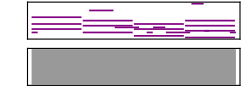

```mathematica
melody = createmelody[newnotes, notedurations];
chords = minorandalusian[rootnote];
Sound[Flatten[{melody,chords}]]
```

Procedure Outline: Users are expected to provide the tempo, root note, scale and chord arrangement information to start the process. With the provided information, the first step is to create a random melody. First the time durations are created for 4 whole notes randomly, then random pitches are assigned to each time duration to form individual notes in the random melody. When the random melody is ready, the notes that are unfit are selected. These unfit notes are altered by using a method that calculates fitness of each note in 2 octave range of scale by weighting these values with their importance and randomness and scaling them with the absolute distance. With this alteration process, the random melody is now in harmony with the chord progression.

Model: 
	Take User Input for tempo, root note, scale and chord arrangement
		tempo is integer,
		root note is an integer between 0 and 11
		scale is selected as minor or major
		chord arrangement selection is dependant on the scale selection
			if scale is minor: chord arrangement is selected as pop progress or Andalusian cadence
			if scale is major: chord arrangement is selected as pop progress, 50’s progress or Andalusian cadence
	Random note durations are created for 4 whole bars in an additive technique
	Random melody is produced by assigning random pitches in 2 octave range of given root to previously calculated time durations
	Random melody notes that are out of the given scale changed with fitter notes.
	The user selected chord progression and the evolved melody are presented together

```mathematica
Harmonize[t_,r_,s_,c_]:=Module[{bpm=t,root=r,scale=s,ca=c},
notedurations = createnotedurations[bpm];
notes = createrandompitches[notedurations,root];
outofscale = getoutofscalenotes[notes,scale];
distances :={0,12,24,5,7,2,scale[[7]],scale[[3]],scale[[4]]}+root;
weights:={1.5,1.5,1.5,1.5,1.5,1.3,1.3,1.2,1.2};
hh = findnotes[distances,weights,outofscale];
newnotes = harmonize[notes,scale, hh];
melody = createmelody[newnotes, notedurations];
chords = ca[root];
Return[Flatten[{melody,chords}]]
];
```

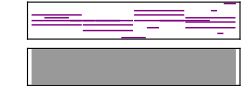

```mathematica
Sound[Harmonize[100,9,minorscale,minorpop]]
```

Validation of the Model: Evaluation of a musical quality of a melody is personal, therefore the model can be validated by comparing a random melody and harmonized melody. To achieve this task, we follow the same procedure presented in the model above but present the random melody (before modification) with given chord progression and harmonized melody with given chord progression. Assuming the given tempo is 96, root note is A, scale is minor and chord arrangement is pop progression; the first output provides the random melody and chord progression together.

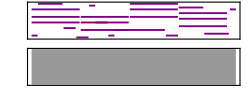

```mathematica
exchords = minorpop[9];
exnotedurations = createnotedurations[96];
exnotes = createrandompitches[exnotedurations, 9];
For[i=1,i<Length[exnotes],i++,If[exnotes[[i]]==-1,exnotes[[i]]=None]];
exmelody = createmelody[exnotes,exnotedurations];
Sound[Flatten[{exmelody,exchords}]]
```

Here we take the random melody and harmonize it, then present it with the chord progression:

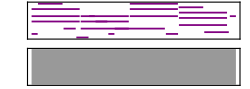

```mathematica
exout = getoutofscalenotes[exnotes,minorscale];
exhh= findnotes[distances,weights,exout];
exnewnotes = harmonize[exnotes,minorscale,exhh];
exnewmelody = createmelody[exnewnotes,exnotedurations];
Sound[Flatten[{exnewmelody,exchords}]]
```

```mathematica
popsel ={0->"C", 1->"C#",2->"D",3->"D#",4->"E",5->"F",6->"F#",7->"G",8->"G#",9->"A",10->"A#",11->"B"};
nn = Harmonize[120,0,majorscale,majorpop];
Harmonization=Panel[
Grid[
{
{"Tempo: ",InputField[Dynamic[t,Initialization->(t=120)],Number,FieldSize->12]},
{"Root Note: ",PopupMenu[Dynamic[rn,Initialization->(rn=0)],popsel,FieldSize->10]},
{"Scale: ",PopupMenu[Dynamic[sc,Initialization->(sc=minorscale)],{minorscale->"min", majorscale->"maj"}, "min",FieldSize->10]},
{"Chord Arrangement: ",Dynamic[PopupMenu[Dynamic[ca,Initialization->(ca=minorpop)], If[sc===minorscale, {minorpop,minorandalusian}, {majorpop,majorandalusian}],FieldSize->10]]},
{Button["Create New Melody", 
nn=Harmonize[First[Dynamic[t]],First[Dynamic[rn]],First[Dynamic[sc]],First[Dynamic[ca]]]
],SpanFromLeft},
{Dynamic[Sound[nn]],SpanFromLeft}
},Alignment->{Right,Left}]];
```

## Results and Discussion

In this section, we present the results for our methods and a Dynamic interactive interface. Our goal is to create random but inspiring melodies for a selected chord progression, we achieved this task with the Harmonization model presented. This model requires some information to produce melodies, these are provided by the user. With given information, our model creates a random melody and than modifies it following the music theory rules. To summarize our method and provide an interactive interface, we present “Harmonization”.

```mathematica
Harmonization
```

Tempo:  | 
Root Note:  | 
Scale:  | 
Chord Arrangement:  | 
Create New Melody | 
 |